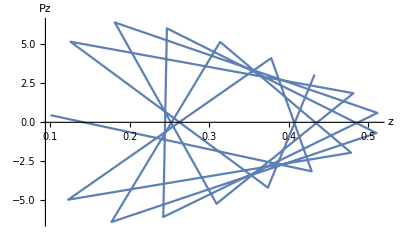

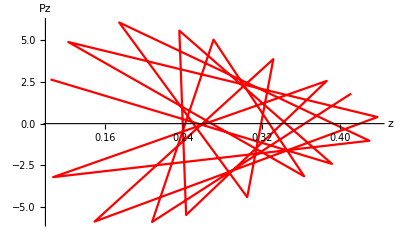

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Print[ListLinePlot[Table[{zm[i,1.8*qcrit[1.3,1,0.1],1.3,1,0.1],pz[i,1.8*qcrit[1.3,1,0.1],1.3,1,0.1]},{i,0.5,8.5,0.5}],AxesLabel->{z,Pz},PlotRange->All]];
Print[ListLinePlot[Table[{zm[i,2.1*qcrit[1.3,1,0.1],1.3,1,0.1],pz[i,2.1*qcrit[1.3,1,0.1],1.3,1,0.1]},{i,0.5,8.5,0.5}],AxesLabel->{z,Pz},PlotRange->All,PlotStyle->Red]];
]
```

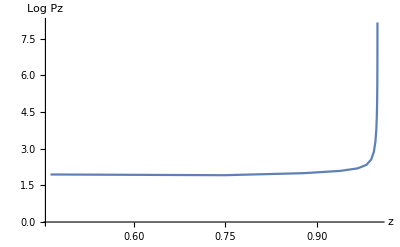

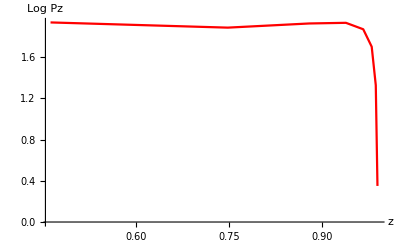

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Print[ListLinePlot[Table[{zm[i,0.99*qcrit[1.3,1,0.1],1.3,1,0.1],pz[i,0.99*qcrit[1.3,1,0.1],1.3,1,0.1]//Log},{i,0.5,8.5,0.5}],AxesLabel->{z,Log Pz},PlotRange->All]];
Print[ListLinePlot[Table[{zm[i,1.00*qcrit[1.3,1,0.1],1.3,1,0.1],pz[i,1.00*qcrit[1.3,1,0.1],1.3,1,0.1]//Log},{i,0.5,8.5,0.5}],AxesLabel->{z,Log Pz},PlotRange->All,PlotStyle->Red]];
]
```